## Mesh

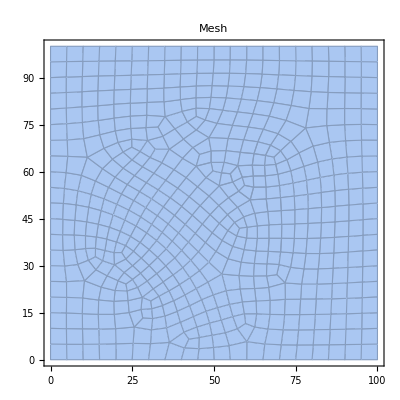

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"mesh_check.csv"}]];
nodeId=First@Position[data,"Nodes: Node_i"][[1]];
elemId=First@Position[data,"Elements: Elem_i"][[1]];
bcId=First@Position[data,"BCs"][[1]];
xyId=First@Position[data,"xy: Node(flattened)"][[1]];
rhoId=First@Position[data,"rho: Node"][[1]];
cId=First@Position[data,"c: Node"][[1]];
nodes=data[[nodeId+1;;elemId-1]];
elems=data[[elemId+1;;bcId-1]];
bcXY=data[[xyId+1;;rhoId-1]];
bcRho=data[[rhoId+1;;cId-1]];
bcC=data[[cId+1;;All]];
mesh=MeshRegion[nodes[[All,2;;3]],Polygon[#]&/@(elems[[All,2;;5]]+1),PlotLabel->Style["Mesh",18],Frame->True,ImageSize->400]
```

#### Show BCs

```mathematica
xFixedList=Select[bcXY[[All,1]],EvenQ]/2+1;
yFixedList=(Select[bcXY[[All,1]],OddQ]+1)/2;
rhoFixedList=bcRho[[All,1]]+1;
cFixedList=bcC[[All,1]]+1;
xBCSymbol=ListPlot[nodes[[#,2;;3]]&/@xFixedList,PlotMarkers->Style["⊳",16],PlotStyle->Red];
yBCSymbol=ListPlot[nodes[[#,2;;3]]&/@yFixedList,PlotMarkers->Style["△",16],PlotStyle->Red];
rhoBCSymbol=ListPlot[nodes[[#,2;;3]]&/@rhoFixedList,PlotMarkers->Style["ρ",16],PlotStyle->Green];
cBCSymbol=ListPlot[nodes[[#,2;;3]]&/@cFixedList,PlotMarkers->Style["c",16],PlotStyle->Yellow];
```

```mathematica
symb={xBCSymbol,yBCSymbol};
Column[{
CheckboxBar[Dynamic[symb],{xBCSymbol->"x",yBCSymbol->"y",rhoBCSymbol->"ρ",cBCSymbol->"c"}],
Dynamic[
Show[HighlightMesh[mesh,Labeled[0,"Index"]],{symb}]
]
}]
```

| x   | y   | ρ   | c

## Phase σ_act vs ρ_i, f_m

```mathematica
phiλData=Import[FileNameJoin[{NotebookDirectory[],"data/stress.csv"}],"Data"];
strPos=Position[phiλData,_String][[All,1]];
contourData=TakeList[phiλData,Differences@strPos];
refList=Flatten[contourData[[All,1]]];
```

```mathematica
Module[{iRef=1},
plotData=Drop[contourData[[iRef]],1];
ListContourPlot[plotData[[All,{1,2,3}]],PlotRange->All,PlotLabel->refList[[iRef]],PlotLegends->Automatic,Contours->{0.00198,0.00414}(*Contours->3*),Mesh->{13,5},MeshFunctions->{#1&,#2&},MeshStyle->Darker[Red]]
]
```

## Analytical Solutions

### Parameters

```mathematica
fiberIndex=1;
fiberRef={"CollagenSvensson1","CollagenSvensson2","FibrinWLiuUncrossForward","FibrinWLiuCrossForward","FibronectinDeraviCirc","FibronectinDeraviSqua","FibronectinDeraviTri"};
kfList={13.5447,16.3434,893.392,3382.2,0.431412,0.598608,0.350922};
k2List={20.5351,19.5505,0.00052392,0.000513122,0.0067476,0.00528002,0.0163591};
k0=0.0511;
kf=kfList[[fiberIndex]];
k2=k2List[[fiberIndex]];
phib=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"PhibCurve","PhibLamb_"<>ToString[fiberRef[[fiberIndex]]]<>"f7.txt"}],"Data"][[All,1;;2]],InterpolationOrder->1];
```

```mathematica
FF[λa_,λs_]:={{λa,0},{0,λs}};
ψf[I1_,I4_,κ_]:=kf/(2 k2)(ⅇ^(k2(κ I1+(1-2κ)I4-1))-k2
(κ I1+(1-2κ)I4-1));
Eb[λa_,λs_,κ_]:=κ(λa^2+λs^2)+(1-2κ)λa^2-1;
matA0[λa_,λs_,κ_,a0_]:=κ IdentityMatrix[2]+(1-2κ)Outer[Times,a0,a0];
matA[λa_,λs_,κ_,a0_]:=FF[λa,λs].matA0[λa,λs,κ,a0].FF[λa,λs]ᵀ;
σact[ϕf_,fm_,ρi_,λa_,λs_,κ_,a0_]:=10^-6 ϕf fm phib[Max[1,Eb[λa,λs,κ]+1]] ρi matA[λa,λs,κ,a0]/Tr[matA[λa,λs,κ,a0]];
σpre[λa_,λs_]:=-k0/(λa^2 λs^2) IdentityMatrix[2];
σpas[ϕf_,λa_,λs_,κ_,a0_]:=1/(1(*θ^p,Volume Change*))FF[λa,λs].(k0 IdentityMatrix[2]+ϕf 2(D[ψf[I1,I4,κ],I1]IdentityMatrix[2]+D[ψf[I1,I4,κ],I4]Outer[Times,a0,a0])).FF[λa,λs]ᵀ/.{I1->λa^2+λs^2,I4->λa^2};
```

### All-fixed Boundary

```mathematica
Module[{
λa=1.07,
λs=1.05,
κ=0.1,
ϕf=1,
fm=7,
ρi=7000,
a0={1,0}
},
Grid[{
{"σ_tot=",MatrixForm[σpre[λa,λs]+σpas[ϕf,λa,λs,κ,a0]+σact[ϕf,fm,ρi,λa,λs,κ,a0]]},
{"σ_pres=",MatrixForm@σpre[λa,λs]},
{"σ_pas=",MatrixForm@σpas[ϕf,λa,λs,κ,a0]},
{"σ_act=",MatrixForm@σact[ϕf,fm,ρi,λa,λs,κ,a0]}
},Alignment->Left,{Dividers->{{True,False,True},All},Spacings->1.5 {1,1}}]
]
```

σ_tot= | (236.822 | 0.
0. | 25.353)
σ_pres= | (-0.0404832 | 0.
0. | -0.0404832)
σ_pas= | (236.843 | 0.
0. | 25.3913)
σ_act= | (0.0201198 | 0.
0. | 0.00215274)

### With Vector Field

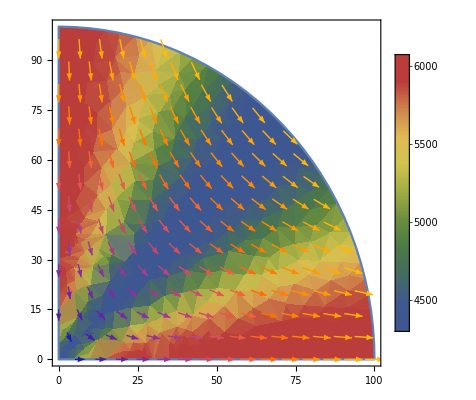

```mathematica
Show[DensityPlot[Norm[Diagonal@σact[1,7,7000,1.07,1.05,0.1,{10x,-10y}/100]] 10^6,{x,y}∈mesh,PlotLegends->Automatic,ColorFunction->"DarkRainbow"],VectorPlot[{x,-y},{x,y}∈mesh,VectorScaling->Automatic,RegionFillingStyle->None,StreamStyle->Darker@Red]]
```

### σ_act vs λ

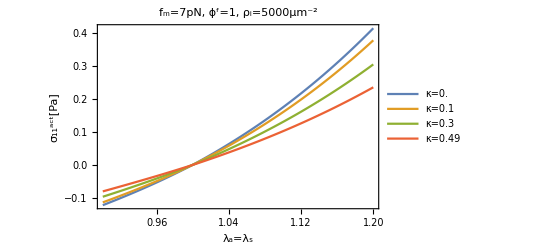

```mathematica
Module[{ϕf=1,fm=7,ρi=5000,a0a0={1,0}},
Plot[Evaluate[(σpre[λ,λ]+σpas[ϕf,λ,λ,#,a0a0]+σact[ϕf,fm,ρi,λ,λ,#,a0a0])[[1,1]]&/@{0.0,0.1,0.3,0.49}],{λ,0.9,1.2},PlotRange->All,Frame->True,FrameLabel->{Style["λ_a=λ_s",16],Style["σ_11^act[Pa]",16]},PlotLabel->Style["f_m="<>ToString[fm]<>"pN, ϕ^f="<>ToString[ϕf]<>", ρ_i="<>ToString[ρi]<>"μm^-2",15],PlotLegends->Evaluate["κ="<>ToString[#]&/@{0.0,0.1,0.3,0.49}],Epilog->{Dashed,Line[{{0,1980},{10,1980}}],Line[{{0,4140},{10,4140}}]}]
]
```

### Varying Fiber Types with Free Outer Curve

```mathematica
Module[{ϕf=1,fm=7,ρi=7000,a0a0={1,0}},deform=FindRoot[{σpre[λa,λs][[1,1]]+σpas[ϕf,λa,λs,0.1,a0a0][[1,1]]==-σact[ϕf,fm,ρi,λa,λs,0.1,a0a0][[1,1]],σpre[λa,λs][[2,2]]+σpas[ϕf,λa,λs,0.1,a0a0][[2,2]]==-σact[ϕf,fm,ρi,λa,λs,0.1,a0a0][[2,2]]},{{λa,0.9},{λs,1.1}}]
]
```

{λa→0.99793,λs→0.848944}

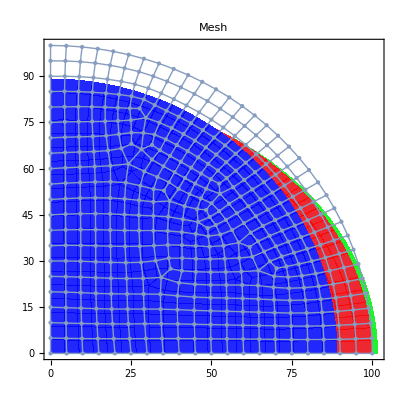

```mathematica
outerPts=bcXY[[All,1]]+1;
Row[{
Show[
MeshRegion[{1.0159821817415726 nodes[[All,2]],0.8422913827639453 nodes[[All,3]]}ᵀ/.deform,Polygon[#]&/@(elems[[All,2;;5]]+1),PlotLabel->Style["Mesh",18],Frame->True,PlotTheme->"Polygons",MeshCellHighlight->{{2,All}->Directive[Green
,Opacity[0.8]]},ImageSize->400],
MeshRegion[{0.9979296572464311 nodes[[All,2]],0.8489441124143022 nodes[[All,3]]}ᵀ/.deform,Polygon[#]&/@(elems[[All,2;;5]]+1),PlotLabel->Style["Mesh",18],Frame->True,PlotTheme->"Polygons",MeshCellHighlight->{{2,All}->Directive[Red,Opacity[0.8]]}],
MeshRegion[{0.8902352869192421 nodes[[All,2]],0.8911719741065675 nodes[[All,3]]}ᵀ/.deform,Polygon[#]&/@(elems[[All,2;;5]]+1),PlotLabel->Style["Mesh",18],Frame->True,PlotTheme->"Polygons",MeshCellHighlight->{{2,All}->Directive[Blue,Opacity[0.8]]}],
MeshRegion[MeshCoordinates[mesh],MeshCells[mesh,1]]
],
SwatchLegend[{ColorData[97,1],Red,Green,Blue},{"Ref","Col","Fibrin","Fibronectin"}]}
]
```